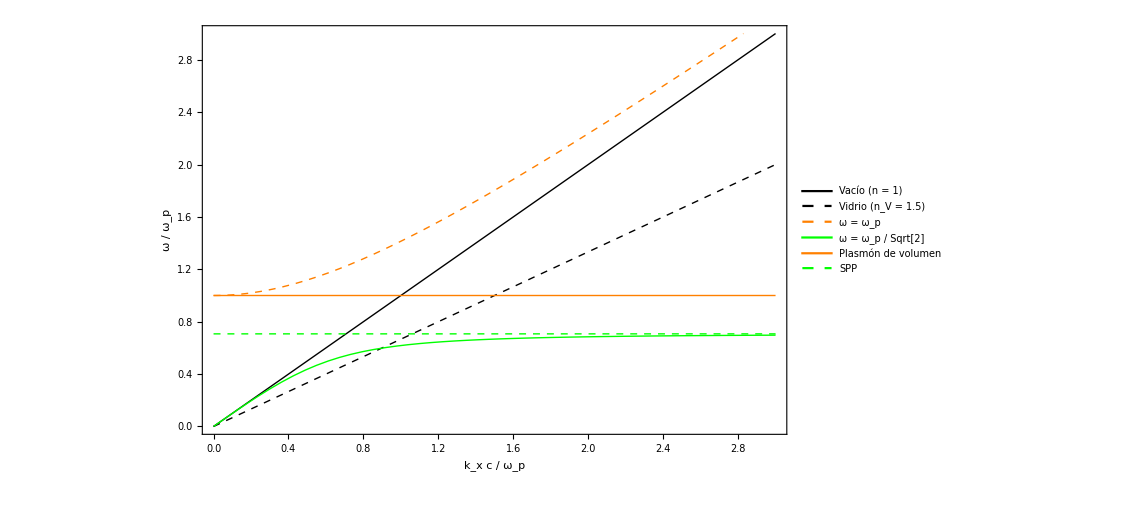

```mathematica
(*Parámetros*)wp=1; (*frecuencia de plasma*)
c=1; (*velocidad de la luz*)
nv=1.5; (*índice de refracción del vidrio*)

(*Ecuaciones de las curvas*)
vacio[kx_]:=kx c/wp;
vidrio[kx_]:=kx c/(nv wp);
volumenPlasmon[kx_]:=Sqrt[(kx c/wp)^2+1];
spp[kx_]:=Sqrt[(kx c/wp)^2+1/2-Sqrt[(kx c/wp)^4+1/4]];

(*Rango de kx*)
kxMax=3;
kxRange={kx,0,kxMax};

(*Gráfica*)
Plot[{vacio[kx],vidrio[kx],volumenPlasmon[kx],spp[kx],wp,wp/Sqrt[2]},kxRange,PlotRange->{{0,kxMax},{0,3}},PlotStyle->{{Black,Thick},(*Línea para el vacío*){Dashed,Black,Thick},(*Línea para el vidrio*){Dashed,Orange,Thick},(*Línea ω=ω_p*){Green,Thick},(*Línea ω=ω_p/Sqrt[2]*){Orange,Thick},(*Línea para el plasmón de volumen*){Dashed,Green,Thick} (*Línea para SPP*)},AxesLabel->{"k_x c / ω_p","ω / ω_p"},Ticks->{{0,1,2,3},{0,1,2,3}},Frame->True,FrameLabel->{"k_x c / ω_p","ω / ω_p"},PlotLegends->{Placed[{"Vacío (n = 1)","Vidrio (n_V = 1.5)","ω = ω_p","ω = ω_p / Sqrt[2]","Plasmón de volumen","SPP"},{Right,Top}]}]
```